## Classes 6

Лабораторная работа №6.

```mathematica
Visualization & Graphics
```

### Data visualization

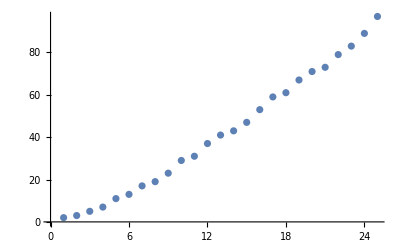

```mathematica
ListPlot[Prime[Range[25]]] (*отображает диаграмму состоящую из простых чисел от 1 до 25*)
```

```mathematica
ListPlot3D[{{1,1,1,1},{1,2,1,2},{1,1,3,1},{1,3,1,4}},Mesh->All] (*отображает высоту точек на поверхности в 3х мерном пространстве*)
```

-Graphics3D-

```mathematica
data=ExampleData[{"Geometry3D","StanfordBunny"},"VertexData"];
```

```mathematica
ListSurfacePlot3D[data,MaxPlotPoints->50] (*строит объект в 3д пространстве записанный в переменной data*)
```

-Graphics3D-

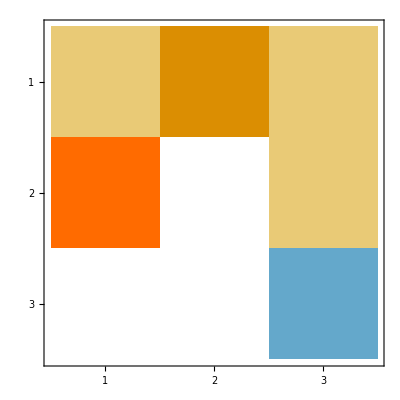

```mathematica
MatrixPlot[{{1,2,1},{3,0,1},{0,0,-1}}] (*отображает значения матрицы в виде ячеек с разным цветовым тоном 0 белый, >0 теплые тона, < 0 холодные тона*)
```

### Function Visualization

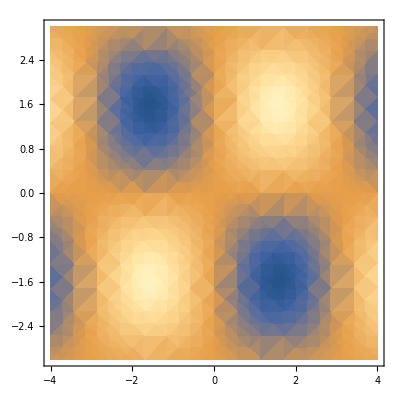

```mathematica
DensityPlot[Sin[x]Sin[y],{x,-4,4},{y,-3,3}]
```

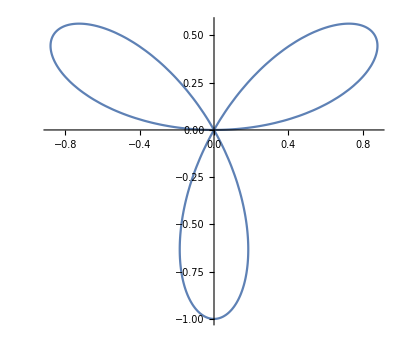

```mathematica
PolarPlot[Sin[3t],{t,0,Pi}]
```

```mathematica
RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2Pi}] (*график поверхности вращения*)
```

-Graphics3D-

### Charts & information Visualization

```mathematica
PairedBarChart[{1,3,5},{2,4,6}] (*отображает спаренную диаграмму*)
```

-Graphics-

### Date & Time Visualization

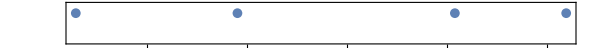

```mathematica
TimelinePlot[{DateObject[{2000,7,31},"Day","Gregorian",-6.],DateObject[{2003,10,23},"Day","Gregorian",-6.],DateObject[{2008,2,25},"Day","Gregorian",-6.],DateObject[{2010,5,17},"Day","Gregorian",-6.]}] (*отображает график с датами в хронологическом порядке*)
```

### Geographic Visualization

```mathematica
GeoListPlot[{Entity["City",{"Brest","Brest","Belarus"}],Entity["City",{"Minsk","Minsk","Belarus"}]}]
```

-Graphics-

```mathematica
GeoGraphics[GeoMarker[],GeoRange->Quantity[1,"Miles"]] (*определяет вашу геолокацию*)
```

-Graphics-

```mathematica
GeoGraphics[Polygon[LinguisticAssistant]](*выделяет на карте выбранную страну*)
```

-Graphics-

### Dynamic Visualization

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}](*manipulate позволяет изменять значение переменной a*)
```